```mathematica
Solve[{x(24-x-2y)==0,y(30-y-2x)==0,x>=0,y>=0},{x,y}]
```

{{x→0,y→0},{x→0,y→30},{x→12,y→6},{x→24,y→0}}

```mathematica
Expand[(-36-l)(-30-l)+60]
```

1140+66 l+l^2

```mathematica
Expand[(-24-l)(-18-l)+48]
```

480+42 l+l^2

```mathematica
24*12
```

288

```mathematica
Expand[(-12-l)(-6-l)-288]
```

-216+18 l+l^2

```mathematica
Solve[x(24-x-2y)==0,y]
```

{{y→(24-x)/2}}

```mathematica
Solve[y(30-y-2x)==0,y]
```

{{y→0},{y→-2 (-15+x)}}

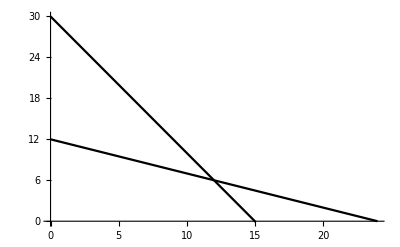

```mathematica
Plot[{(24-x)/2,-2(-15+x)},{x,0,24},PlotRange->{Automatic,{-0.1,30}},PlotStyle->Black]
```

```mathematica
Eigenvalues[{{-36,0},{-60,-30}}]
```

{-36,-30}

```mathematica
Eigenvalues[{{-24,-48},{ 0,-18}}]
```

{-24,-18}

```mathematica
Eigenvalues[{{-12,-24 },{-12,-6}}]//N
```

{-26.2337,8.23369}

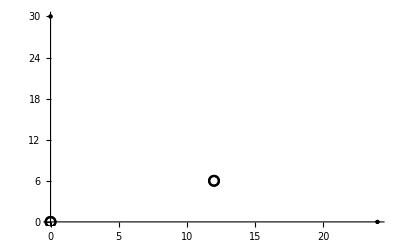

```mathematica
ListPlot[List/@{{0,0},{0,30},{24,0},{12,6}},PlotStyle->Directive[Black,PointSize[Large]],PlotMarkers->{{Graphics[Circle[]],Medium},None,None,{Graphics[Circle[]],Medium}}]
```

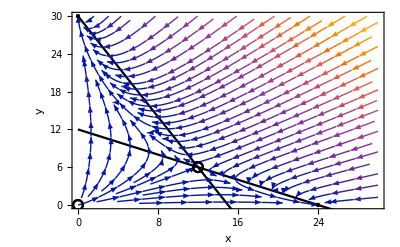

```mathematica
Show[{Plot[{(24-x)/2,-2(-15+x)},{x,0,30},PlotStyle->Black,Frame->True,FrameLabel->{"x","y"}],ListPlot[List/@{{0,0},{0,30},{24,0},{12,6}},PlotStyle->Directive[Black,PointSize[Large]],PlotMarkers->{{Graphics[Circle[]],Medium},None,None,{Graphics[Circle[]],Medium}}],StreamPlot[{x(24-x-2y),y(30-y-2x)},{x,0,30},{y,0,30}]},PlotRange->{{0,30},{0,30}}]
```